## Andrews Plots

For a high-dimensional data point x={x_1,x_2,...,x_d} in R^d the Andrews plot defines:
f_x(t)=x_1/(√2)+x_2 sin(t)+x_3 cos(2)+x_4 sin(2t)+x_5 cos(2t)+...
which projects the data onto:
(1/(√2),sin(t),cos(t),sin(2t),cos(2t),...). The curve is plotted over the interval -π < t < π.

```mathematica
t=ToExpression[StringSplit/@ReadList["\\\\wsl$\\ubuntu\\mnt\\hfscr\\xyz_128_298K.xyz","String"][[3;;]]][[All,2;;]];
```

```mathematica
AndrewsCurve[row_List,t_]:=Module[{n=Length[row]},row[[1]]/Sqrt[2]+Sum[row[[k]]*Which[EvenQ[k],Sin[(k/2) t],OddQ[k],Cos[((k-1)/2) t]],{k,2,n}]]
```

```mathematica
AndrewsPlot[data_,opts:OptionsPattern[]]:=Module[{t},Plot[Evaluate@Table[AndrewsCurve[data[[i]],t],{i,Length[data]}],{t,-Pi,Pi},PlotRange->All,Evaluate@FilterRules[{opts},Options[Plot]]]]
```

This plots the Andrews curve for 6 atoms of 2 different water molecules. The atoms that are part of the same water give curves that are similar.

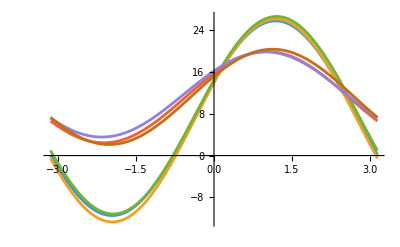

```mathematica
AndrewsPlot[t[[1;;6]]]
```

Standardizing the data improves spread.

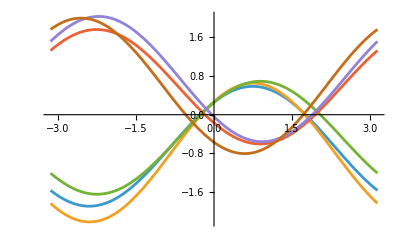

```mathematica
AndrewsPlot[Transpose[Standardize/@Transpose[t[[1;;6]]]]]
```